Carbapenem Resistance

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

#### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="United States"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
years = Drop[data[[1]],1]; 
tt = Length[years]; 
isolates=Drop[data[[3]],1]; 
resistance=Drop[data[[4]],1];
rfreq=resistance/isolates; (*Resistance frequency*)
cn = Drop[data[[5]],1]/10000; (*consumption*)
pc = 0.21; (*proportion of carbapanem prescription out of all antibiotics prescribed for bacterial pneuomonia NOTE: Update with better estimate.*)
tc = cn/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
p=cn/tc; (*proportion of bacterial pneumonia recieving carbapanem*)
```

#### Model

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.
The functional form of the model is e^m/(1/r_0-1+e^m)

```mathematica
r[t_,r0_,a_,b_] := ⅇ^(a* Total[cn[[1;;t]]]+b*t)/((1/r0)-1+ⅇ^(a* Total[cn[[1;;t]]]+b*t)) ; (*dA/dt= Subscript[R, C] CA + Subscript[R, N] A, dB/dt= Subscript[N, C] CB + Subscript[N, N] B=> m = a ∑_(i=1)^t Subscript[p, t] Subscript[C, t] + bt and  a = Subscript[R, C]-Subscript[N, C], b=Subscript[R, N]-Subscript[N, N]*)
```

```mathematica
Maximum Likelihood Function
```

Note: The likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.

```mathematica
Lik[r0_,a_,b_]:= Total[Table[Log[Binomial[isolates[[j]],resistance[[j]]]]+resistance[[j]]*Log[r[j-1,r0,a,b]]+(isolates[[j]]-resistance[[j]])*Log[1-r[j-1,r0,a,b]],{j,1,tt}]]
```

#### Model Fitting

Using NMaximize function to optimize the likelihood function defined above.

```mathematica
{max,{fr0,fa,fb}}=NMaximize[{Lik[r0,a,b],0< r0< 1, a≥ 0, b≤ 0},{r0,a,b}, MaxIterations->10000]
```

{-158.072,{r0→0.00205465,a→72.5067,b→-1.11733×10^-12}}

#### Plots

Putting together observed and fitted data together for plotting.

```mathematica
t=Range[1,tt]; 
res=Transpose@{years,rfreq}; (*resistance frequency data*)
x = Table[r[j,fr0[[2]],fa[[2]],fb[[2]]],{j,1,tt}];
fit=Transpose@{years,x};
fit
```

{{2000.,0.00251598},{2001.,0.00319394},{2002.,0.004264},{2003.,0.00573169},{2004.,0.00786866},{2005.,0.0111078},{2006.,0.0162281},{2007.,0.0239894},{2008.,0.0363311},{2009.,0.0558016},{2010.,0.0853531},{2011.,0.13088},{2012.,0.196644}}

Show plots

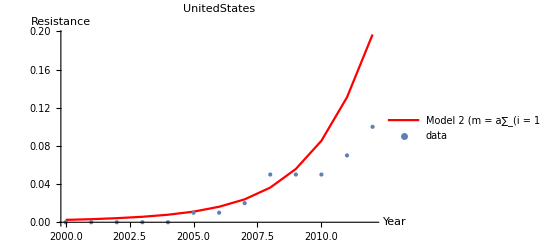

```mathematica
plotD=ListPlot[{res}, PlotStyle-> PointSize[Large],PlotRange-> All,PlotLegends->{"data"}];
plotM = ListLinePlot[fit, PlotStyle-> {Red},AxesLabel->{Year,Resistance},PlotRange-> All,PlotLabel-> UnitedStates,PlotLegends->{"Model 2 (m = a∑_(i = 1)^t  c_i + b t)"}];

Show[plotM,plotD]
```